Autor: Karolina Tatarczyk

# Metody numeryczne w technice

## (kierunek Matematyka)

## Projekt 1

Metody Rungego-Kutty

Napisać procedury realizujące algorytmy metod Rungego-Kutty rzędu trzeciego i rzędu czwartego (argumenty:  f, x_0, y_0, h, n).

Korzystając z napisanych procedur wyznaczyć rozwiązanie przybliżone zagadnienia początkowego:

{y'(x)=(x y(x) - y^2(x))/x^2,
y(1)=2.

Obliczenia wykonać dla 20 kroków o długości 0.1.

Na wspólnym rysunku wykreślić rozwiązanie dokładne oraz uzyskane rozwiązania przybliżone.
Wykreślić także, na jednym rysunku, błędy uzyskanych rozwiązań przybliżonych.

## Rozwiązanie

### Tworzenie procedur

```mathematica
RungeKutty3[function_,X0_,Y0_,H_,number_]:=Module[{f=function, x0=X0, y0=Y0,h=H,n=number,x,y},
x={x0};
y={y0};
For[i=1,i≤n,i++,
AppendTo[x,x[[i]]+h];
k1= f[x[[i]],y[[i]]];
k2=f[x[[i]]+h/2, y[[i]]+h*k1/2];
k3=f[x[[i+1]], y[[i]]-h*k1+2*h*k2];
AppendTo[y, y[[i]]+h*(k1+4*k2+k3)/6];
];
Return[Transpose[{x,y}]]
]
```

```mathematica
RungeKutty4[function_,X0_,Y0_,H_,number_]:=Module[{f=function, x0=X0, y0=Y0,h=H,n=number,x,y},
x={x0};
y={y0};
For[i=1,i≤n,i++,
AppendTo[x,x[[i]]+h];
k1= f[x[[i]],y[[i]]];
k2=f[x[[i]]+h/2, y[[i]]+h*k1/2];
k3=f[x[[i]]+h/2, y[[i]]+h*k2/2];
k4=f[x[[i+1]],y[[i]]+h*k3];
AppendTo[y, y[[i]]+h*(k1+2*k2+2*k3+k4)/6];
];
Return[Transpose[{x,y}]]
]
```

### Obliczenie funkcji wyznaczonymi metodami

```mathematica
f[x_,y_]:=(x*y-y^2)/x^2;
x0=1;
y0=2;
h=0.1;
n=20;
rk3=RungeKutty3[f,x0,y0,h,n]
rk4=RungeKutty4[f,x0,y0,h,n]
```

{{1,2},{1.1,1.84781},{1.2,1.75876},{1.3,1.70529},{1.4,1.67376},{1.5,1.65667},{1.6,1.64954},{1.7,1.64954},{1.8,1.6548},{1.9,1.66402},{2.,1.6763},{2.1,1.69096},{2.2,1.70752},{2.3,1.7256},{2.4,1.74491},{2.5,1.76523},{2.6,1.78637},{2.7,1.80819},{2.8,1.83057},{2.9,1.85343},{3.,1.87668}}

{{1,2},{1.1,1.84777},{1.2,1.75869},{1.3,1.70521},{1.4,1.67369},{1.5,1.6566},{1.6,1.64947},{1.7,1.64947},{1.8,1.65473},{1.9,1.66395},{2.,1.67623},{2.1,1.6909},{2.2,1.70746},{2.3,1.72554},{2.4,1.74485},{2.5,1.76517},{2.6,1.78631},{2.7,1.80813},{2.8,1.83052},{2.9,1.85337},{3.,1.87662}}

### Wykresy przedstawiające wyniki działania procedur oraz rozwiązanie dokładne

```mathematica
plot1=ListPlot[rk3,PlotStyle->{Red}];
plot2=ListPlot[rk4];
```

```mathematica
result=DSolve[{y'[x] == (x*y[x]-y[x]^2)/x^2,y[1]==2}, y[x], x][[1,1,2]];
plot3=Plot[result,{x,1,3}];
```

```mathematica
Show[plot1,plot2,plot3]
```

-Graphics-

### Obliczenie i przedstawienie błędów uzyskanych rozwiązań

```mathematica
ListX=Transpose[rk3][[1]];
ListY3=Transpose[rk3][[2]];
ListY4=Transpose[rk4][[2]];
```

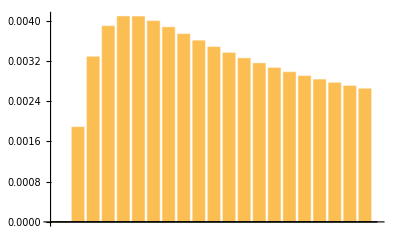

```mathematica
resultPoints =  Table[result /. {x -> ListX[[i]]}, {i, 1, Length[ListX]}] ;
bladbezwzgledny =  Abs[ListY3 - resultPoints] ;
bladwzgledny = 100 * bladbezwzgledny / Abs[resultPoints];
bar3=BarChart[bladwzgledny]
```

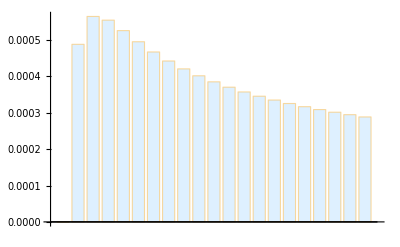

```mathematica
resultPoints =  Table[result /. {x -> ListX[[i]]}, {i, 1, Length[ListX]}] ;
bladbezwzgledny =  Abs[ListY4 - resultPoints] ;
bladwzgledny = 100 * bladbezwzgledny / Abs[resultPoints];
bar4=BarChart[bladwzgledny, ChartStyle->LightBlue]
```

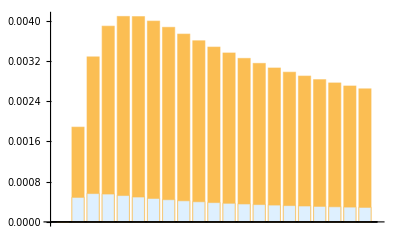

```mathematica
Show[{bar3,bar4},PlotLegends->{"bar1","bar2"}]
```

```mathematica
(*pomarańczowy - błędy podczas działania procedury Rungego-Kuttego rzędu 3, niebieski - błędy podczas działania procedury Rungego-Kuttego rzędu 4*)
```